# Computing Expected Number of Steps in a Random Walk

### Original Graph

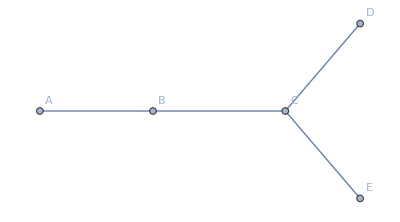

```mathematica
Graph[{"A"<->"B","B"<->"C", "C"<->"D","C"<->"E"},VertexLabels->"Name",GraphLayout->"SpringElectricalEmbedding"]
```

### Markov Chain

```mathematica
transitionTable=({{0, 1/2, 0, 0, 0}, {1, 0, 1/3, 0, 0}, {0, 1/2, 0, 1, 1}, {0, 0, 1/3, 0, 0}, {0, 0, 1/3, 0, 0}});
start=({{1}, {0}, {0}, {0}, {0}});
end=({{0}, {0}, {0}, {1}, {0}});
```

```mathematica
MatrixPower[transitionTable, 3].start//N
```

{{0.},{0.666667},{0.},{0.166667},{0.166667}}

```mathematica
Eigenvalues[transitionTable] (* Eigenvalue of 1 exists, so we have a steady state vector *)
```

{-1,1,-1/(√3),1/(√3),0}

```mathematica
Eigenvectors[transitionTable,2] (* Find the eigenvector/steady-state vector of e-value 1 *)
```

{{-1,2,-3,1,1},{1,2,3,1,1}}

```mathematica
#/Total[#]&[{1,2,3,1,1}] (* Normalize *)
```

{1/8,1/4,3/8,1/8,1/8}

```mathematica
(* Verify I'm not full of shit *)
transitionTable.%==%
```

True

So I managed to find the steady state vector of this matrix, but when multiplying the matrix by large powers, it oscillates between two vectors... so that’s fun.
I don’t think this helped me solve my “expected number of steps” yet though...

```mathematica
MatrixPower[transitionTable,11]//MatrixForm
```

(0 | 61/243 | 0 | 121/486 | 121/486
122/243 | 0 | 364/729 | 0 | 0
0 | 182/243 | 0 | 365/486 | 365/486
121/486 | 0 | 365/1458 | 0 | 0
121/486 | 0 | 365/1458 | 0 | 0)

```mathematica
%[[4,1]]//N
```

0.248971

```mathematica
Sum[MatrixPower[transitionTable,i][[1,4]],{i,1,11}]//N (* Guess #1: Expected steps = 11, cause that's when this sum goes to >1? But then why aren't they symmetric? *)
```

1.12551

```mathematica
Sum[MatrixPower[transitionTable,i][[4,1]],{i,1,11}]//N
```

1.12551

Or, from the lecture notes I just found, we can setup a system of linear equations.
Let E_j be the expected number of steps in the random walk before reaching “D” when current at “j” (j={A,B,C,D,E})
Then clearly, E_D=0, and δ_AD=E_A (δ_AD=expected number of steps to go from A to D)

```mathematica
Solve[{Ed==0,
	Ec==1+1/3 Eb+1/3 Ed+1/3 Ee,
	Ee==1+1*Ec,
	Eb==1+1/2 Ea+1/2 Ec,
	Ea==1+1*Eb},{Ea,Eb,Ec,Ed,Ee}]
```

{{Ea→11,Eb→10,Ec→7,Ed→0,Ee→8}}

```mathematica
(* Looks like it worked! *)
```

Lets do the same thing again, but now E_j is the expected number of steps before reading “A” when at j, and we want E_D

```mathematica
Solve[{Ed==1+1*Ec,
	Ec==1+1/3 Eb+1/3 Ed+1/3 Ee,
	Ee==1+1*Ec,
	Eb==1+1/2 Ea+1/2 Ec,
	Ea==0},{Ea,Eb,Ec,Ed,Ee}]
```

{{Ea→0,Eb→7,Ec→12,Ed→13,Ee→13}}